# 1 a) Building Equations and Matrices

Numerical Linear Algebra underlies almost every technical computation.  It is how one equations are encoded and solved.

## Fitting Data

Suppose I have a bunch of points from a function and I want to run a polynomial p through the points!

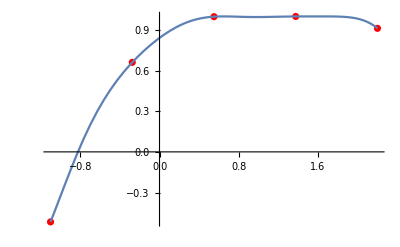

```mathematica
f[x_]:=Sin[x+ Cos[x Sin[x]]]
{a,b}={-1.1,2.2};m=5;
xs=Table[x,{x,a,b,(b-a)/(m-1)}];
fs=Map[f,xs];
Data=Transpose[{xs,fs}];
Show[ListPlot[Data,PlotStyle->Red],Plot[f[x],{x,a,b}]]
```

The polynomial is simply a sum p[x]=a_0+a_1 x+a_2 x^2+… We have m points we should be able to choose m constants to go through the m points. The m equations are 
	a_0 | + | a_1 x_1 | + | a_1 x_1^1 | + | a_2 x_1^2 | + | … | + | a_(m-1)x_1^(m-1) | = | f(x_1)
a_0 | + | a_1 x_2 | + | a_1 x_2^1 | + | a_2 x_2^2 | + | … | + | a_(m-1)x_2^(m-1) | = | f(x_2)
  |   |   |   |   |   |   |   |   |   |   | ⋮ |  
a_0 | + | a_1 x_m | + | a_1 x_m^1 | + | a_2 x_m^2 | + | … | + | a_(m-1)x_m^(m-1) | = | f(x_m)

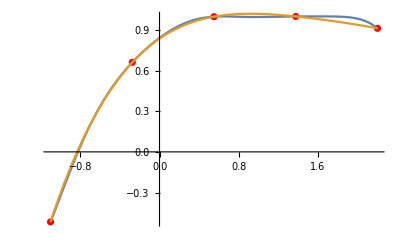

```mathematica
A=Table[x^(j-1),{x,xs},{j,m}]; 
MatrixForm[A];
as=LinearSolve[A,fs];
p[x_]=Sum[as[[j]] x^(j-1),{j,1,m}];
Show[ListPlot[Data,PlotStyle->Red],Plot[{f[x],p[x]},{x,a,b}]]
```